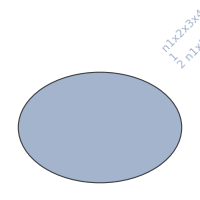
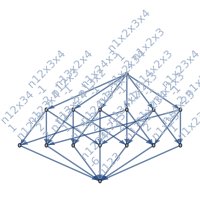
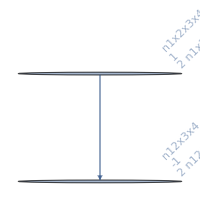
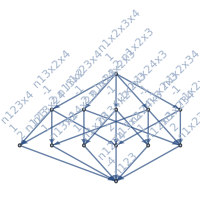
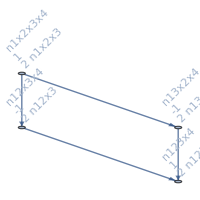
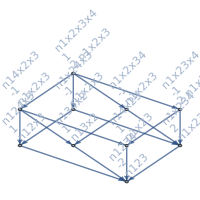
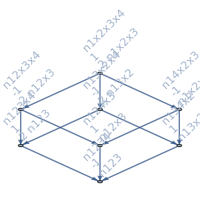
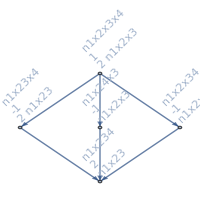
-Graphics-0 | -Graphics- | -Graphics-
-Graphics-243 | -Graphics- | -Graphics-
-Graphics-324 | -Graphics- | -Graphics-
-Graphics-351 | -Graphics- | -Graphics-
-Graphics-360 | -Graphics- | -Graphics-
-Graphics-363 | -Graphics- | -Graphics-
-Graphics-364 | -Graphics- | -Graphics-
-Graphics-361 | -Graphics- | -Graphics-
-Graphics-354 | -Graphics- | -Graphics-
-Graphics-355 | -Graphics- | -Graphics-
-Graphics-352 | -Graphics- | -Graphics-
-Graphics-333 | -Graphics- | -Graphics-
-Graphics-336 | -Graphics- | -Graphics-
-Graphics-337 | -Graphics- | -Graphics-
-Graphics-334 | -Graphics- | -Graphics-
-Graphics-327 | -Graphics- | -Graphics-
-Graphics-328 | -Graphics- | -Graphics-
-Graphics-325 | -Graphics- | -Graphics-
-Graphics-270 | -Graphics- | -Graphics-
-Graphics-279 | -Graphics- | -Graphics-

```mathematica
With[
{all=allGraphs4, size=200},
TableForm[
Table[
With[{comp=FindComplement[k,all]},
{Labeled[all[k,"graph"],k],Show[MobiusGraph4[k,all],ImageSize->{size,size}],Show[MobiusGraph4[comp,all],ImageSize->{size,size}]}
],
{k,Take[Select[Keys[all],With[{g=all[#,"graph"]},VertexCount[g]==VertexCount[all[0,"graph"]] ]&],20]}
]
]
]
```